## NF theory with non-homogeneous production (field)

```mathematica
eval=Thread[{ka,kb,α,β,γ,Da,Db}->{1,1,0.25,0.25,-0.05,1,4}]
```

{ka→1,kb→1,α→0.25,β→0.25,γ→-0.05,Da→1,Db→4}

```mathematica
j={{-ka,0,1},{0,-kb,1},{α,-β,γ}};
jd=j-k^2DiagonalMatrix[{Da,Db,0}];
```

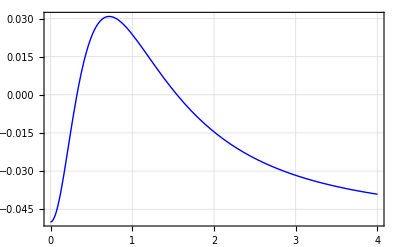

```mathematica
Plot[Max[Re[Eigenvalues[jd/.eval]]],{k,0,4},PlotStyle->{Thick,Blue},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

#### Numerical solution

```mathematica
T=5000;
```

```mathematica
eqn={D[a[t,x],{t,1}]==c[t,x]-ka a[t,x]+Da D[a[t,x],{x,2}]-a[t,x]^3+0.001Cos[x],D[b[t,x],{t,1}]==c[t,x]-kb b[t,x]+Db D[b[t,x],{x,2}]-b[t,x]^3,D[c[t,x],{t,1}]==α a[t,x]-β b[t,x]+γ c[t,x]-c[t,x]^3}/.eval;
ic={a[0,x]==0,b[0,x]==0.3(-Cos[x]+Sin[x]),c[0,x]==0};
bc={a[t,-Pi]==a[t,Pi],b[t,-Pi]==b[t,Pi],c[t,-Pi]==c[t,Pi]};
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,-Pi,Pi}];//Quiet
```

```mathematica
frames=Table[Plot[{asol[t,x](*,bsol[t,x],csol[t,x]*)},{x,-Pi,Pi},PlotStyle->{Thick,RGBColor[0,0,0.9]},PlotRange->{-0.12,0.12},BaseStyle->{FontFamily->"CMU Serif",14},Frame->True],{t,1,T,100}];
ListAnimate[frames]
```

```mathematica
z=Table[1/(2Pi )NIntegrate[Exp[-I x]asol[i,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{i,1,T,20}];
```

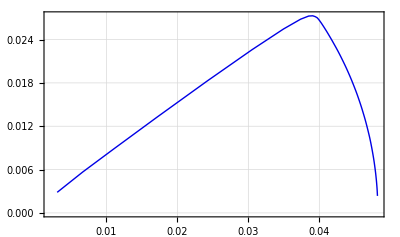

```mathematica
fieldtraj=ListLinePlot[Table[{Re[z[[i]]],Im[z[[i]]]},{i,1,250}],PlotRange->All,Frame->True,PlotStyle->{Thick,RGBColor[0,0,0.9]},AspectRatio->True,BaseStyle->{FontFamily->"CMU Serif",14},Frame->True,GridLines->Automatic]
```

#### r and θ extracted from the data and fit to NF equation. Evolution along the radial (r) direction is fast compared with angular (θ) direction.

```mathematica
rdata=Sqrt[Re[z[[1;;20]]]^2+Im[z[[1;;20]]]^2];
```

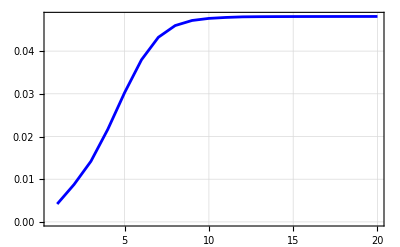

```mathematica
ListLinePlot[rdata,PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Blue]
```

```mathematica
times=Table[i,{i,Dimensions[rdata][[1]]}];
rtofit=Table[{times[[i]],rdata[[i]]},{i,Dimensions[rdata][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[rtofit,functofit,{{r0,0.1},{p1,01},{p2,0.01}},x]
```

FittedModel[…]

```mathematica
param=fit["BestFitParameters"]
```

{r0→0.0033305,p1→0.490101,p2→212.559}

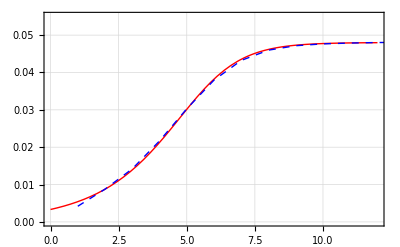

```mathematica
rfit=Show[Plot[functofit/.param,{x,0,12},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"CMU Serif",14}],ListLinePlot[rdata,PlotStyle->{Thick,Dashed,Blue},BaseStyle->{FontFamily->"CMU Serif",14}],Frame->True,GridLines->Automatic,PlotRange->{{0,12},{0,0.055}}]
```

```mathematica
rt=functofit/.param/.x->t
```

(0.00333854 ⅇ^(0.490101 t))/(√(1+0.00483401 ⅇ^(0.980202 t)))

```mathematica
csp=ComplexStreamPlot[p1 z-p2 z Abs[z]^2+0.0006/.param,{z,0.055I,0.055},StreamScale->Full,StreamColorFunction->None,AspectRatio->True,StreamStyle->RGBColor[0.4,0.4,0.4]];
```

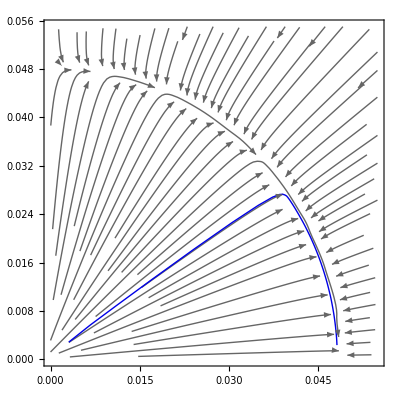

```mathematica
fieldgeometry=Show[csp,fieldtraj]
```

```mathematica
data=Table[{i,ArcTan[Im[z[[i]]]/Re[z[[i]]]]},{i,250}];
```

```mathematica
nlm=NonlinearModelFit[data,2ArcTan[Tan[a]Exp[b t]],{{a,-0.3},{b,-0.01}},t]
```

FittedModel[…]

```mathematica
θparam=nlm["BestFitParameters"]
```

{a→0.341171,b→-0.0109324}

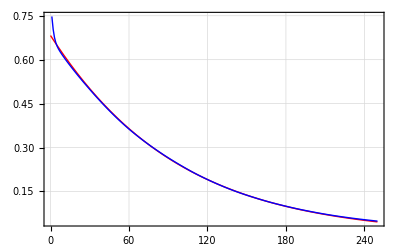

```mathematica
anglefit=Show[Plot[2ArcTan[Tan[a]Exp[b t]]/.nlm["BestFitParameters"],{t,0,250},PlotRange->All,PlotStyle->{Thick,Red}],ListLinePlot[data,PlotStyle->{Thick,Blue}],Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",FontSize->14}]
```

#### Fitting the physical solution at three timepoints

```mathematica
{t1,t2,t3}={5,20,200};
```

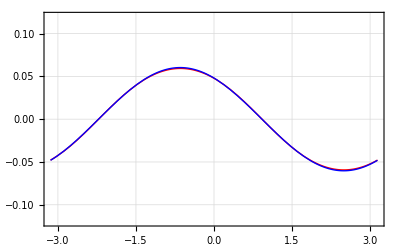

```mathematica
plt1=Plot[{asol[20(t1-1),x],rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]+Conjugate[rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]]/.t->t1/.nlm["BestFitParameters"]},{x,-Pi,Pi},PlotRange->{-0.12,0.12},Frame->True,GridLines->Automatic,PlotStyle->{{Thick,Red},{Thick,Blue}},BaseStyle->{FontFamily->"CMU Serif",FontSize->14}]
```

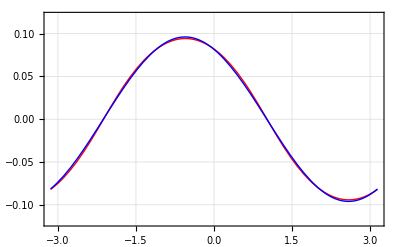

```mathematica
plt2=Plot[{asol[20(t2-1),x],rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]+Conjugate[rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]]/.t->t2/.nlm["BestFitParameters"]},{x,-Pi,Pi},PlotRange->{-0.12,0.12},Frame->True,GridLines->Automatic,PlotStyle->{{Thick,Red},{Thick,Blue}},BaseStyle->{FontFamily->"CMU Serif",FontSize->14}]
```

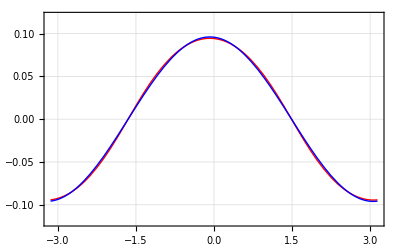

```mathematica
plt3=Plot[{asol[20(t3-1),x],rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]+Conjugate[rt Exp[I 2ArcTan[Tan[a]Exp[b t]]]Exp[I x]]/.t->t3/.nlm["BestFitParameters"]},{x,-Pi,Pi},PlotRange->{-0.12,0.12},Frame->True,GridLines->Automatic,PlotStyle->{{Thick,Red},{Thick,Blue}},BaseStyle->{FontFamily->"CMU Serif",FontSize->14}]
```